You can write any text inside Mathematica documents. 
Various forms of brackets:

In Mathematica:
[] => function arguments

```mathematica
Sin[Pi]
```

0

() => specifying the order of operations (mathematical parentheses)

```mathematica
(1+1)*2
```

4

{} => lists
[[ ]] => indexes for a list

```mathematica
x = {10,20,30,40,50};
```

```mathematica
x[[3]]
```

30

<| |> => associations (i.e., dictionaries in Python)

```mathematica
d=<||>;
```

```mathematica
d["name"]="Hiroki"
```

Hiroki

```mathematica
d
```

<|name→Hiroki|>

```mathematica
Values[d]
```

{Hiroki}

In Python:
[] => lists, indexes for a list, list comprehension
() => function arguments, tuples
{} => dictionaries, sets

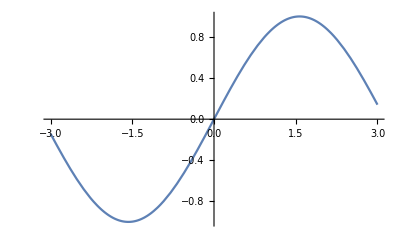

```mathematica
Plot[Sin[x],{x,-3,3}]
```

```mathematica
Clear[x];
```

```mathematica
∫_(-∞)^∞ Cos[x]/(ⅇ^(x^2))ⅆx
```

(√π)/ⅇ^(1/4)

```mathematica
∫Cos[x]/(ⅇ^(x^2))ⅆx
```

```mathematica
Sin[x y]
```

```mathematica
Plot3D[Sin[x y],{x,0,4},{y,0,4},PlotStyle->Red]
```

-Graphics3D-

```mathematica
x={"Hello",1,20.3,1+ⅈ,{10,20,30}};
```

```mathematica
x[[1]]
```

Hello

```mathematica
x[[5]]
```

{10,20,30}

```mathematica
x[[-1]]
```

{10,20,30}

```mathematica
x[[1]]="hello";
```

```mathematica
x
```

{hello,1,20.3,1+ⅈ,{10,20,30}}

```mathematica
x[[1;;3]]
```

{hello,1,20.3}

```mathematica
x[[;;3]]
```

{hello,1,20.3}

```mathematica
x[[-3;;]] (* this is a comment *)
```

{20.3,1+ⅈ,{10,20,30}}

```mathematica
(* this is a comment *)
```

```mathematica
A={{1,2,3},{4,5,6},{7,8,0}};
```

```mathematica
A//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 0)

```mathematica
A//Det
```

27

```mathematica
B={{1,2,3}};
B=B//Transpose;
B//MatrixForm
```

(1
2
3)

```mathematica
A.B
```

{{14},{32},{23}}

```mathematica
Eigenvalues[A]
```

{Root[-27-72 #1-6 #1^2+#1^3&,3],Root[-27-72 #1-6 #1^2+#1^3&,1],Root[-27-72 #1-6 #1^2+#1^3&,2]}

```mathematica
#^2&[{1,2,3}]
```

{1,4,9}

```mathematica
Sin[{1,2,3}]
```

{Sin[1],Sin[2],Sin[3]}

```mathematica
Eigenvalues[A]//N
```

{12.1229,-5.73451,-0.388384}

```mathematica
Eigenvectors[A]//N
```

{{0.468482,1.10544,1.},{-0.314248,-0.441847,1.},{8.02758,-7.07268,1.}}

```mathematica
N[Pi,1000]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

```mathematica
data=Import["http://chart.finance.yahoo.com/table.csv?s=GOOG&a=0&b=14&c=2017&d=1&e=14&f=2017&g=d&ignore=.csv"];
```

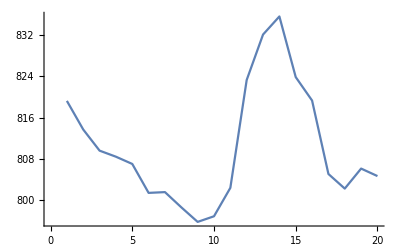

```mathematica
data[[2;;,5]]//ListLinePlot
```

```mathematica
Clear[x];
```

```mathematica
Reduce[x^2+x^3-2x<0,x]
```

x<-2||0<x<1

```mathematica
i=1;
While[i<10,
Print["hello",i];
i += 1;
]
```

hello1

hello2

hello3

hello4

hello5

hello6

hello7

hello8

hello9

```mathematica
data=RandomReal[{0,1},{100,2}];
```

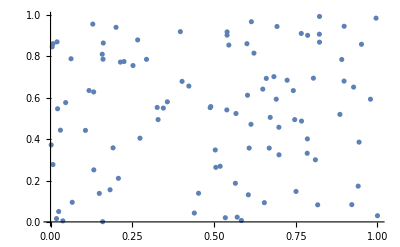

```mathematica
ListPlot[data]
```

```mathematica
FindClusters[data]
```

```mathematica
{{{0.26648602022740864,0.8794984618966308},{0.021548069706042616,0.5467365540264153},{0.12922121010551524,0.9559560480239082},{0.21378721899320863,0.7723598181729256},{0.10678073886706763,0.44223423824232255},{0.29351849274685593,0.7857486146772878},{0.1491251087824843,0.13769879423102394},{0.34496147255554055,0.5500751244476683},{0.3970538670397781,0.9195173850136646},{0.16132546402220838,0.864538219962919},{0.43980465620328735,0.042829013173551145},{0.32624349152465815,0.5531572709057218},{0.04631046801166283,0.5766839437405162},{0.06636742070798429,0.09479234091040256},{0.0627083414964491,0.7884996195454337},{0.11774942239097141,0.6349744433034563},{0.22474971258175236,0.7750586645998367},{0.03757793464780823,0.005105470730792039},{0.01827719928687288,0.01597057544377911},{0.15811826419771724,0.8102677459818792},{0.20758281258332656,0.21062135609280097},{0.452729885431425,0.13839394770270874},{0.0050460352567576194,0.8463099671299896},{0.40233271115993374,0.6791147284060546},{0.19121358398014365,0.3579747338220822},{0.16054632713154504,0.7863980251106395},{0.15945826696980703,0.0008911878551662866},{0.13187739333338677,0.6281774951535917},{0.01991333125847783,0.8701317324450981},{0.0075398481515278615,0.8611833905073776},{0.35726665027082216,0.580259424897178},{0.007437626684236642,0.27726793072818134},{0.13235269187757304,0.2514168153873646},{0.4230933654426192,0.6565385780057906},{0.03017596488911467,0.4433464791698647},{0.024894924271851027,0.05025827642415748},{0.27351447105674564,0.40460261611393733},{0.25221509689365673,0.7556967687552691},{0.32892439073273616,0.4945483178478307},{0.0020032562867755566,0.37195262384740646},{0.2003345000607506,0.940510344548591},{0.18205610022851637,0.1552813010745424}},{{0.5837392802397123,0.006748452115994175},{0.9214767854080215,0.08341705124273013},{0.8226568182390659,0.8687372318433337},{0.4900742838891581,0.5574335971717357},{0.5188107793843839,0.2688735902157666},{0.5346354727353404,0.020192133020619174},{0.898067712501796,0.9454936457373841},{0.6689237409643378,0.35673238676887276},{0.5671294576843862,0.5238814418171494},{0.9956849606582878,0.9848385674261084},{0.4882702515196784,0.5520449171927371},{0.804016276732237,0.6946162865909222},{0.5055186164177143,0.2636045627056389},{0.822686574646204,0.9929295812381798},{0.5391902484175255,0.5412463689349949},{0.7855625393969385,0.40119573553656096},{0.9436695943457483,0.3855435393483768},{0.6988366559358785,0.32422737644702404},{0.6926875529272449,0.9444265496068263},{0.7426099811638862,0.6346573350727429},{0.6049781245460897,0.13092210125110837},{0.5653789623299994,0.1866776012977036},{0.6832138669314445,0.7019998687536533},{0.5453898689955388,0.8546571640219021},{0.7676782202472339,0.48728141069333897},{0.6903390539187977,0.5931475450157719},{0.613102332948992,0.4716520327675544},{0.8907332861139228,0.7849182666062053},{0.6024326456363025,0.6122272572964558},{0.7669525602140839,0.9108198283422748},{0.6491792459639973,0.6417599323807359},{0.7468450463255523,0.49429555125648306},{0.8977845183529529,0.6805798789680386},{0.88513632389952,0.5195728625918077},{0.600761088732916,0.8612776731572824},{0.8222808366879379,0.9071207816383362},{0.9410053945804466,0.1728883800600307},{0.9510361714027784,0.8583807355510524},{0.926942494725046,0.6514953206190459},{0.7863981519879573,0.9016312628270131},{0.5038622112932976,0.34758170673550404},{0.978567217150881,0.5930209778015618},{0.5400760829940856,0.9183391658962139},{0.5709366210780382,0.0228500514559149},{0.622178376404863,0.815647893379414},{0.8170825761525315,0.08242869147130549},{0.6599085450316851,0.6934627279938026},{0.6539627572041133,0.09294971553534448},{0.9999690946343143,0.02984744064261191},{0.785066642703949,0.3316511151073658},{0.723674964174353,0.6847292206898989},{0.6143145510675696,0.9675464047650757},{0.5399648614786956,0.9026788712312481},{0.6719729871619713,0.5051124341579774},{0.810118467196759,0.3002390388269427},{0.6075662324849862,0.35684291894541853},{0.6984386787166426,0.4574646839101244},{0.750849605695106,0.14706185255332782}}}


Sin[Pi]===0
```

{{{0.266486,0.879498},{0.0215481,0.546737},{0.129221,0.955956},{0.213787,0.77236},{0.106781,0.442234},{0.293518,0.785749},{0.149125,0.137699},{0.344961,0.550075},{0.397054,0.919517},{0.161325,0.864538},{0.439805,0.042829},{0.326243,0.553157},{0.0463105,0.576684},{0.0663674,0.0947923},{0.0627083,0.7885},{0.117749,0.634974},{0.22475,0.775059},{0.0375779,0.00510547},{0.0182772,0.0159706},{0.158118,0.810268},{0.207583,0.210621},{0.45273,0.138394},{0.00504604,0.84631},{0.402333,0.679115},{0.191214,0.357975},{0.160546,0.786398},{0.159458,0.000891188},{0.131877,0.628177},{0.0199133,0.870132},{0.00753985,0.861183},{0.357267,0.580259},{0.00743763,0.277268},{0.132353,0.251417},{0.423093,0.656539},{0.030176,0.443346},{0.0248949,0.0502583},{0.273514,0.404603},{0.252215,0.755697},{0.328924,0.494548},{0.00200326,0.371953},{0.200335,0.94051},{0.182056,0.155281}},{{0.583739,0.00674845},{0.921477,0.0834171},{0.822657,0.868737},{0.490074,0.557434},{0.518811,0.268874},{0.534635,0.0201921},{0.898068,0.945494},{0.668924,0.356732},{0.567129,0.523881},{0.995685,0.984839},{0.48827,0.552045},{0.804016,0.694616},{0.505519,0.263605},{0.822687,0.99293},{0.53919,0.541246},{0.785563,0.401196},{0.94367,0.385544},{0.698837,0.324227},{0.692688,0.944427},{0.74261,0.634657},{0.604978,0.130922},{0.565379,0.186678},{0.683214,0.702},{0.54539,0.854657},{0.767678,0.487281},{0.690339,0.593148},{0.613102,0.471652},{0.890733,0.784918},{0.602433,0.612227},{0.766953,0.91082},{0.649179,0.64176},{0.746845,0.494296},{0.897785,0.68058},{0.885136,0.519573},{0.600761,0.861278},{0.822281,0.907121},{0.941005,0.172888},{0.951036,0.858381},{0.926942,0.651495},{0.786398,0.901631},{0.503862,0.347582},{0.978567,0.593021},{0.540076,0.918339},{0.570937,0.0228501},{0.622178,0.815648},{0.817083,0.0824287},{0.659909,0.693463},{0.653963,0.0929497},{0.999969,0.0298474},{0.785067,0.331651},{0.723675,0.684729},{0.614315,0.967546},{0.539965,0.902679},{0.671973,0.505112},{0.810118,0.300239},{0.607566,0.356843},{0.698439,0.457465},{0.75085,0.147062}}}

```mathematica
True
0===0.
```

True

False

```mathematica
clear[x]
```

clear[x]

```mathematica
x->0
```

x→0

```mathematica
Plot[Sin[x],{x,-2,2}
PlotStyle->Black,Filling->0]
```

System`ProtoPlotDump`iPlot[Plot,System`ProtoPlotDump`obj$5046,Sin[x],{PlotStyle x,-2 PlotStyle,2 PlotStyle}→GrayLevel[0],Filling→0]

```mathematica
Clear[x]
```

```mathematica
(a x^2 +b x +c)/.{Plus -> x}
```

x[c,b x,a x^2]

```mathematica
a x^2+b x+c
```

```mathematica
a x^2+b x+c
%/.c->10
```

c+b x+a x^2

```mathematica
{1,2,"hi",{4,5,6,1},100.,-10,"hello"}/. {x_String :> x <> "s"}
```

```mathematica
{1,2,"his",{4,5,6,1},100.,-10,"hellos"}

s =Solve[a x^2 + b x + c ==0,x]
```

{1,2,his,{4,5,6,1},100.,-10,hellos}

```mathematica
{{x->(-b-√(b^2-4 a c))/(2 a)},{x->(-b+√(b^2-4 a c))/(2 a)}}

(a x^2 + b x + c)/.s
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

ReplaceAll::reps: {s} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

c+b x+a x^2/.s

```mathematica
Manipulate[
Plot[{Sin[ x],sin[b x], Sin[a x] +Sin[b x], {x, 0, 10}}]
,{a,0,20}
,{b,0,20}

]
```